# Dispersion relations and low relaxation of spin waves in thin magnetic films

## Constants

```mathematica
(*Plank's constant*)
ℏ =6.582119569*10^-16 ;(*eV sec*) 
ℏSI = 1.054571817 10^-34;(*Joules seconds*)
(*Bohr magneton*)
μb=5.7883818060 10^-5; (*eV per Tesla*)
μbSI = 9.2740100657 10^-24;(*Joules per Tesla*)
(*Vacuum permeability*)
μ0 = 1.256637 10^-6; (*Newton per Ampere squared*)
(*Spin*)
S=1/2;
(*Lande factor*)
g=2; (*from google*)
(*The gyromagnetic ratio*)
γ = g μb /ℏ;
γSI = g μbSI /ℏ;
(*Inverse temperature*)
k=8.617333262 10^-5;(*eV per Kelvin*)(*Boltzman constant*)
T=100;(*Kelvin*)(*Temperature*)
β= 1/(k T);
(*Lattice distance*)
a=3.508 10^-10;(*meters*)(*Ref:"CrSBr: an air-stable, two-dimensional magnetic semiconductor"*)
Sa =a^2; (*See Equation (17)*)
(*Distance between layers*)
d=7.959 10^-10;(*meters*)(*Ref:"CrSBr: an air-stable, two-dimensional magnetic semiconductor"*)
(*Inter-layer coupling, i.e. coupling in the same layer.*)
I0=- 3.38 10^-3; (*eV*)(*Ref: "Spin Waves and Magnetic Exchange Hamiltonian for CrSBr"*)
(*Intra-layer coupling, i.e. coupling between diferent layers.*)
Id =0.05 10^-3; (*eV*)
(*External magetic field*)
H=0.5;(*Tesla*)
```

### Scaling

```mathematica
(*magnetic energy*)
{ g μbSI, (g μbSI)/(g μbSI)}
(*spin-spin exchange, same layer*)
{I0 (1.602176 10^-19), I0 (1.602176 10^-19)/(g μbSI) }
(*spin-spin exchange, different layer*)
{Id(1.602176 10^-19), Id(1.602176 10^-19)/(g μbSI)}
(*Dipole energy*)
{(μ0 (g μbSI)^2)/a^3, (μ0 (g μbSI)^2)/(a^3(g μbSI))}
(*lattice spacing: in layer, out of layer*)
{a, d, a/a, d/a}
(*Boltzman weight*)
{1/k,  (g μb)/(k)}
```

{1.8548×10^-23,1.}

{-5.41535×10^-22,-29.1964}

{8.01088×10^-24,0.431899}

{1.00144×10^-23,0.539919}

{3.508×10^-10,7.959×10^-10,1.,2.26881}

{11604.5,1.34343}

## Hamiltonian

### Operators

```mathematica
(*Spin 3/2 operators*)
Sx=N[1/2{{0, √3, 0, 0}, {√3, 0, 2, 0}, {0, 2, 0, √3}, {0, 0, √3, 0}}];
Sy=N[1/(2I){{0, √3, 0, 0}, {-√3, 0, 2, 0}, {0, -2, 0, √3}, {0, 0, -√3, 0}}];
Sz=N[{{3/2, 0, 0, 0}, {0, 1/2, 0, 0}, {0, 0, -1/2, 0}, {0, 0, 0, -3/2}}];
Sp=N[{{0, √3, 0, 0}, {0, 0, 2, 0}, {0, 0, 0, √3}, {0, 0, 0, 0}}];
Sm=N[{{0, 0, 0, 0}, {√3, 0, 0, 0}, {0, 2, 0, 0}, {0, 0, √3, 0}}];
Sop = Table[{KroneckerProduct[IdentityMatrix[4^(k-1)],  Sx, IdentityMatrix[4^(8-k)]],KroneckerProduct[IdentityMatrix[4^(k-1)], Sy, IdentityMatrix[4^(8-k)]], KroneckerProduct[IdentityMatrix[4^(k-1)],  Sz, IdentityMatrix[4^(8-k)]] }, {k, 1, 8}];
SopI0 = Table[{KroneckerProduct[IdentityMatrix[4^(k-1)],I0 Sx, IdentityMatrix[4^(8-k)]],KroneckerProduct[IdentityMatrix[4^(k-1)], I0 Sy, IdentityMatrix[4^(8-k)]], KroneckerProduct[IdentityMatrix[4^(k-1)], I0 Sz, IdentityMatrix[4^(8-k)]] }, {k, 1, 8}];
SopId = Table[{KroneckerProduct[IdentityMatrix[4^(k-1)], Id Sx, IdentityMatrix[4^(8-k)]],KroneckerProduct[IdentityMatrix[4^(k-1)], Id Sy, IdentityMatrix[4^(8-k)]], KroneckerProduct[IdentityMatrix[4^(k-1)], Id Sz, IdentityMatrix[4^(8-k)]] }, {k, 1, 8}];
Ham = Sum[Sum[SopI0[[k]][[j]].Sop[[k+1]][[j]], {j, 1, 3}], {k, 1, 3}] + Sum[SopI0[[4]][[j]].Sop[[1]][[j]], {j, 1, 3}]+Sum[Sum[SopI0[[k]][[j]].Sop[[k+1]][[j]], {j, 1,3}], {k, 5, 7}] +Sum[SopI0[[8]][[j]].Sop[[5]][[j]], {j, 1, 3}]+
Sum[Sum[SopId[[k]][[j]].Sop[[k+4]][[j]], {j, 1,3}], {k, 1, 4}] + Sum[KroneckerProduct[IdentityMatrix[4^(k-1)], H*Sz, IdentityMatrix[4^(8-k)]], {k, 1, 8}];
```

```mathematica
(*Eigenvalues*)
Evals = Eigenvalues[Ham];
```

```mathematica
ListPlot[Sort[Evals, Less]]
```

```mathematica
(*Partition Function for the Gibbs ensemble*)
Z = Sum[Exp[- β Evals[[k]]], {k, 1, Length[Evals]}]//N
```

```mathematica
(*Eigenvectors*)
Evecs = Eigenvectors[Ham];
```

```mathematica
(*Normalized Eigenvectors*)
Evecs = Map[Function[x, x/Norm[x]], Evecs];
```

```mathematica
(*Average Sz over the Gibbs ensemble*)
AvgSz = Table[(1/Z)Sum[Transpose[Evecs[[j]]]. Sop[[k]][[3]].Evecs[[j]]Exp[- β Evals[[j]]], {j, 1, Length[Evecs]}], {k, 1, 8}];
AvgSz
```

```mathematica
(*Spin 1/2 operators*)
Sx= (1/2){{0, 1}, {1, 0}};
Sy= (1/2){{0, I}, {-I,0 }};
Sz= (1/2){{1, 0}, {0,-1}};
Sop = Table[{KroneckerProduct[IdentityMatrix[2^(k-1)],  Sx, IdentityMatrix[2^(8-k)]],KroneckerProduct[IdentityMatrix[2^(k-1)], Sy, IdentityMatrix[2^(8-k)]], KroneckerProduct[IdentityMatrix[2^(k-1)],  Sz, IdentityMatrix[2^(8-k)]] }, {k, 1, 8}];
SopI0 = Table[{KroneckerProduct[IdentityMatrix[2^(k-1)],I0 Sx, IdentityMatrix[2^(8-k)]],KroneckerProduct[IdentityMatrix[2^(k-1)], I0 Sy, IdentityMatrix[2^(8-k)]], KroneckerProduct[IdentityMatrix[2^(k-1)], I0 Sz, IdentityMatrix[2^(8-k)]] }, {k, 1, 8}];
SopId = Table[{KroneckerProduct[IdentityMatrix[2^(k-1)], Id Sx, IdentityMatrix[2^(8-k)]],KroneckerProduct[IdentityMatrix[2^(k-1)], Id Sy, IdentityMatrix[2^(8-k)]], KroneckerProduct[IdentityMatrix[2^(k-1)], Id Sz, IdentityMatrix[2^(8-k)]] }, {k, 1, 8}];
```

```mathematica
(*Hamiltonian*)
Ham = Sum[Sum[SopI0[[k]][[j]].Sop[[k+1]][[j]], {j, 1, 3}], {k, 1, 3}] + Sum[SopI0[[4]][[j]].Sop[[1]][[j]], {j, 1, 3}]+Sum[Sum[SopI0[[k]][[j]].Sop[[k+1]][[j]], {j, 1,3}], {k, 5, 7}] +Sum[SopI0[[8]][[j]].Sop[[5]][[j]], {j, 1, 3}]+
Sum[Sum[SopId[[k]][[j]].Sop[[k+4]][[j]], {j, 1,3}], {k, 1, 4}] + Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], H*Sz, IdentityMatrix[2^(8-k)]], {k, 1, 8}];
```

```mathematica
(*Eigenvalues*)
Evals = Eigenvalues[Ham];
```

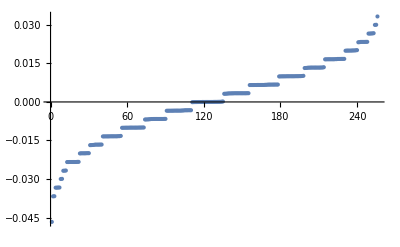

```mathematica
ListPlot[Sort[Evals, Less]]
```

```mathematica
(*Partition Function for the Gibbs ensemble*)
Z = Sum[Exp[- β Evals[[k]]], {k, 1, Length[Evals]}]//N
```

1250.57

```mathematica
(*Eigenvectors*)
Evecs = Eigenvectors[Ham];
```

```mathematica
(*Normalized Eigenvectors*)
Evecs = Map[Function[x, x/Norm[x]], Evecs];
```

```mathematica
(*Average Sx over the Gibbs ensemble*)
AvgSx = Table[(1/Z)Sum[Transpose[Evecs[[j]]]. Sop[[k]][[1]].Evecs[[j]] Exp[- β Evals[[j]]], {j, 1, Length[Evecs]}], {k, 1, 8}];
```

```mathematica
AvgSx
```

{-6.47237×10^-27+0. ⅈ,-2.04109×10^-26+0. ⅈ,-7.47643×10^-27+0. ⅈ,-9.5915×10^-27+0. ⅈ,2.08383×10^-27+0. ⅈ,5.18776×10^-27+0. ⅈ,-5.84127×10^-27+0. ⅈ,-1.86966×10^-26+0. ⅈ}

```mathematica
(*Average Sy over the Gibbs ensemble*)
AvgSy = Table[(1/Z)Sum[Transpose[Evecs[[j]]]. Sop[[k]][[2]].Evecs[[j]]Exp[- β Evals[[j]]], {j, 1, Length[Evecs]}], {k, 1, 8}];
```

```mathematica
AvgSy
```

{0.+1.72417×10^-43 ⅈ,0.+2.47999×10^-43 ⅈ,0.-1.17499×10^-43 ⅈ,0.-2.45461×10^-43 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
(*Average Sz over the Gibbs ensemble*)
AvgSz = Table[(1/Z)Sum[Transpose[Evecs[[j]]]. Sop[[k]][[3]].Evecs[[j]]Exp[- β Evals[[j]]], {j, 1, Length[Evecs]}], {k, 1, 8}];
```

```mathematica
AvgSz
```

{-0.264531+0. ⅈ,-0.267614+0. ⅈ,-0.269145+0. ⅈ,-0.264049+0. ⅈ,-0.264531+0. ⅈ,-0.267614+0. ⅈ,-0.269145+0. ⅈ,-0.264049+0. ⅈ}

### Exchange magnetic field

```mathematica
(*units of Tesla*)
```

```mathematica
Hex =(1/(g μb)){I0 AvgSx[[4]]  + I0 AvgSx[[2]]+ Id AvgSx[[5]], I0 AvgSx[[1]]  + I0 AvgSx[[3]]+ Id AvgSx[[6]], I0 AvgSx[[2]]  + I0 AvgSx[[4]]+ Id AvgSx[[7]], I0 AvgSx[[3]]  + I0 AvgSx[[1]]+ Id AvgSx[[8]], I0 AvgSx[[8]]  + I0 AvgSx[[6]]+ Id AvgSx[[1]], I0 AvgSx[[5]]  + I0 AvgSx[[7]]+ Id AvgSx[[2]], 
I0 AvgSx[[6]]  + I0 AvgSx[[8]]+ Id AvgSx[[3]],
I0 AvgSx[[7]]  + I0 AvgSx[[5]]+ Id AvgSx[[4]]}
```

{2.86364×10^-16+0. ⅈ,-1.83835×10^-16+0. ⅈ,2.90527×10^-16+0. ⅈ,-1.79249×10^-16+0. ⅈ,-3.04306×10^-15+0. ⅈ,-6.48498×10^-16+0. ⅈ,-3.04224×10^-15+0. ⅈ,-6.36869×10^-16+0. ⅈ}

```mathematica
Hey =(1/(g μb)){I0 AvgSy[[4]]  + I0 AvgSy[[2]]+ Id AvgSy[[5]], I0 AvgSy[[1]]  + I0 AvgSx[[3]]+ Id AvgSx[[6]], I0 AvgSy[[2]]  + I0 AvgSy[[4]]+ Id AvgSy[[7]], I0 AvgSy[[3]]  + I0 AvgSy[[1]]+ Id AvgSy[[8]], I0 AvgSy[[8]]  + I0 AvgSy[[6]]+ Id AvgSy[[1]], I0 AvgSy[[5]]  + I0 AvgSy[[7]]+ Id AvgSy[[2]], 
I0 AvgSy[[6]]  + I0 AvgSy[[8]]+ Id AvgSy[[3]],
I0 AvgSy[[7]]  + I0 AvgSy[[5]]+ Id AvgSy[[4]]}
```

{0.+5.25226×10^-32 ⅈ,-1.09383×10^-16+2.27907×10^-32 ⅈ,0.+5.26472×10^-32 ⅈ,0.+7.44976×10^-32 ⅈ,0.-1.8076×10^-32 ⅈ,0.+9.05164×10^-33 ⅈ,0.-1.85038×10^-32 ⅈ,0.+7.0147×10^-33 ⅈ}

```mathematica
Hez =(1/(g μb)){I0 AvgSz[[4]]  + I0 AvgSz[[2]]+ Id AvgSz[[5]], I0 AvgSz[[1]]  + I0 AvgSz[[3]]+ Id AvgSz[[6]], I0 AvgSz[[2]]  + I0 AvgSz[[4]]+ Id AvgSz[[7]], I0 AvgSz[[3]]  + I0 AvgSz[[1]]+ Id AvgSz[[8]], I0 AvgSz[[8]]  + I0 AvgSz[[6]]+ Id AvgSz[[1]], I0 AvgSz[[5]]  + I0 AvgSz[[7]]+ Id AvgSz[[2]], 
I0 AvgSz[[6]]  + I0 AvgSz[[8]]+ Id AvgSz[[3]],
I0 AvgSz[[7]]  + I0 AvgSz[[5]]+ Id AvgSz[[4]]}
```

{28.9805+0. ⅈ,28.9805+0. ⅈ,28.9805+0. ⅈ,28.9805+0. ⅈ,28.9805+0. ⅈ,28.9805+0. ⅈ,28.9805+0. ⅈ,28.9805+0. ⅈ}

## Spin waves in magnetic bilayer

## Normal magnetized films

```mathematica
S=3/2;
(*Hm is the depolarizing magnetic field given by Equation (10)*)
Hm = -0.025;
(*He is the exchange field given by Equation (10)*)
He= -0.025;
(*Hc is the self-consistent field*)
Hc = Hm + He;
(*Brillouin function Subscript[B, S][p] and B[p] = S Subscript[B, S][S p]*)
B[p_]:= (S +1/2)Coth[(S +1/2)p] - 1/2 Coth[p/2];
p = β g μb Abs[H + Hc];
(*σm is the surface magnetic moment density*)
σm= g μb B[p]/Sa;
q = √(qx^2 + qy^2);
(*Equation (21)*)
Ω[qx_, qy_, qz_]:= γ (H + Hm) + (2 B[p] I0)/ℏ(2 - Cos[qx a] - Cos[qy a])
(*Dispersion relation given by Equation (23)*)
ω1[qx_, qy_, qz_] := (Ω[qx, qy, qz](Ω[qx, qy, qz] + 2π γ σm  √(qx^2+qy^2)(1 + Exp[- √(qx^2+qy^2) d])))^(1/2)
ω2[qx_, qy_, qz_] := ((Ω[qx, qy, qz] + (2 B[p] Id)/ℏ)(Ω[qx, qy, qz]+ (2 B[p] Id)/ℏ + 2π γ σm √(qx^2+qy^2)(1 + Exp[- √(qx^2+qy^2) d])))^(1/2)
```

```mathematica
ω1[qx_, qy_, qz_] := (Ω[qx, qy, qz](Ω[qx, qy, qz] + 2π ((g^2 μbSI^2 B[p]μ0)/(Sa ℏSI) ) √(qx^2+qy^2)(1 + Exp[- √(qx^2+qy^2) d])))^(1/2)
ω2[qx_, qy_, qz_] := ((Ω[qx, qy, qz] + (2 B[p] Id)/ℏ)(Ω[qx, qy, qz]+ (2 B[p] Id)/ℏ + 2π ((g^2 μbSI^2 B[p]μ0)/(Sa ℏSI))√(qx^2+qy^2)(1 - Exp[- √(qx^2+qy^2) d])))^(1/2)
```

```mathematica
γ (H + Hm) 
 (2 B[p] I0)/ℏ
 (2 B[p] Id)/ℏ
(g^2 μbSI^2 B[p] μ0)/((d/50) Sa ℏSI)
```

8.3544×10^10

-7.76092×10^10

1.14807×10^9

1.58144×10^10

```mathematica
Ω[0, 0, 0]/10^9
ω1[0,0, 10]/10^9
ω2[10^3,-10^3, 10]/10^9
```

83.544

83.544

84.692

```mathematica
WNscale=10^10;(*Wave number scaling, 1/lattice spacing*)
Fscale=10^9;(*Frequency scaling, GHz*)
Plot3D[{ω1[qx WNscale,qy WNscale, 0]/Fscale, ω2[qx WNscale,qy WNscale, 0]/Fscale}, {qx, -1, 1}, {qy, -1 , 1 }, PlotRange->Full, AxesLabel->{"k_x (10^10/meters)", "k_y, (10^10/meters)", "ω, (GHz)"}, PlotLabel->"Dispersion Relation"]
Plot3D[{ω1[qx WNscale,qy WNscale, 0]/Fscale, ω2[qx WNscale,qy WNscale, 0]/Fscale}, {qx, -1/2, 1/2}, {qy, -1/2 , 1/2 }, PlotRange->Full, AxesLabel->{"k_x (10^10/meters)", "k_y, (10^10/meters)", "ω, (GHz)"}, PlotLabel->"Dispersion Relation"]
```

-Graphics3D-

-Graphics3D-

```mathematica
WNscale=10^10;(*Wave number scaling, 1/lattice spacing*)
Fscale=10^9;(*Frequency scaling, GHz*)
Plot3D[ω2[qx WNscale,qy WNscale, 0]/Fscale, {qx, -1, 1}, {qy, -1 , 1 }, PlotRange->Full, AxesLabel->{"k_x (10^10/meters)", "k_y, (10^10/meters)", "ω, (GHz)"}, PlotLabel->"Dispersion Relation"]
Plot3D[ω2[qx WNscale,qy WNscale, 0]/Fscale, {qx, -1/2, 1/2}, {qy, -1/2 , 1/2 }, PlotRange->Full, AxesLabel->{"k_x (10^10/meters)", "k_y, (10^10/meters)", "ω, (GHz)"}, PlotLabel->"Dispersion Relation"]
```

-Graphics3D-

-Graphics3D-

```mathematica
scale=2 10^3;
Plot3D[Re[ω1[qx,qy, 0]]/10^9, {qx, -scale ,scale}, {qy, -scale , scale }]
Plot3D[ ω2[qx,qy, 0]/10^9, {qx, -scale , scale}, {qy, -scale , scale }, PlotRange->{{-scale, scale}, {-scale, scale}, {84, 85}}]
Plot3D[ Re[ω1[qx,qy, 0]-ω2[qx,qy, 0]]/10^9, {qx, -scale , scale}, {qy, -scale , scale }]
Plot3D[{ω1[qx,qy, 0]/10^9, ω2[qx,qy, 0]/10^9}, {qx, -scale, scale}, {qy, -scale , scale }, PlotRange->Full]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Plot3D[ω1[qx,qy, 10 d]/10^9, {qx, -2 a, 2a}, {qy, -2 a, 2 a}]
Plot3D[ ω2[qx,qy, 10 d]/10^9, {qx, -2 a, 2a}, {qy, -2 a, 2 a}]
Plot3D[{ω1[qx,qy, 10 d]/10^9, ω2[qx,qy, 10 d]/10^9}, {qx, -2 a, 2a}, {qy, -2 a, 2 a}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-